```mathematica
rFunc[invS_]:=√((1/invS)/π);
sFunc[r_]:=N[(π r^2)];
invSFunc[r_]:=1./(π r^2);
```

```mathematica
minTerminalVilliRadius=25mkm;
maxTerminalVilliRadius=80mkm;
maxNonStemVilliRadius=300mkm;
areaFunc[radius_]:=π (radius/mkm)^2;
```

```mathematica
sectionName="2775";

curDir=NotebookDirectory[];
statFile="E:\\06_New cuts of the first sections\\"<>sectionName<>"\\results\\_"<>sectionName<>"_Total_Villous_regions_statistics.csv";



data01=Import[statFile,"Table",FieldSeparators->";"];
dataNames=data01[[1]];
data02=data01[[2;;-1]];
```

```mathematica
data01//Dimensions;
(data02//Dimensions )[[1]]
dataNames
```

2665

{Villous region number,Surface (ÂµmÂ.b2),Perimeter (Âµm),Perimeter_contact (Âµm),Perimeter_frame (Âµm),Nb_IVS_Inside_Region,IVS_Area_Inside_Region (ÂµmÂ.b2),IVS_Perimeter_Inside_Region (Âµm),Nb_Fetal_Capillaries_Inside,Fetal_Capillaries_Area_Inside (ÂµmÂ.b2),FetalCapillariesPerimeter (Âµm)}

```mathematica
areaData=data02[[;;,2]];
perimeterData=data02[[;;,3]];
surfaceDensityData=perimeterData/areaData*1000; (* in mm^-1 *)
σData=perimeterData^2/areaData/(4π);
rInData=2*areaData/perimeterData; (* in μm^-1 *)
rSData=√(areaData/π); (* in μm^-1 *)
```

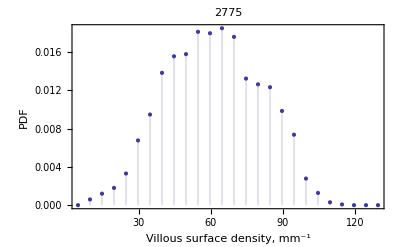

```mathematica
(* Surface density distribution histogram *)
intervalOfInterest={Min[surfaceDensityData]*0.8,Max[surfaceDensityData]*1.2};
selectedSurfaceDensityData=Select[surfaceDensityData,#>=intervalOfInterest[[1]]&&#<=intervalOfInterest[[2]]&];
surfaceDensityBinSize={5};
distribSurfaceDensity=HistogramDistribution[selectedSurfaceDensityData,surfaceDensityBinSize];
pdfSurfaceDensity=PDF[distribSurfaceDensity,s];

pdfSurfaceDensityHistogramPlot=DiscretePlot[pdfSurfaceDensity,{s,intervalOfInterest[[1]],intervalOfInterest[[2]],surfaceDensityBinSize[[1]]},PlotRange->All,Frame->{{True,False},{True,False}},FrameLabel->{"Villous surface density, mm^-1","PDF"},BaseStyle->{FontSize->20}, PlotLabel->sectionName]
(*Show[pdfSurfaceDensityHistogramPlot,
Graphics[{
{Orange,Line[{{areaFunc[minTerminalVilliRadius],0},{areaFunc[minTerminalVilliRadius],0.0004}}]},
{Darker[Red],Line[{{areaFunc[maxTerminalVilliRadius],0},{areaFunc[maxTerminalVilliRadius],0.0004}}]},
{Darker[Green],Line[{{areaFunc[maxNonStemVilliRadius],0},{areaFunc[maxNonStemVilliRadius],0.0004}}]}
}
]]*)

(* Orange - minimal terminal villus,
Red - maximal terminal villus radius,
Green - maximal stem villus radius *)
```

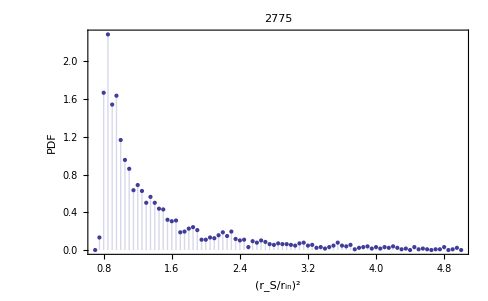

```mathematica
(* Plotting the diagram of the radii ration distribution *)
twoRadiiRatio2List=twoRadiiRatioList^2;
intervalOfInterest={0.7,5+0 *Max[twoRadiiRatio2List]};
selectedTwoRadiiRatio2Data=Select[twoRadiiRatio2List,#>=intervalOfInterest[[1]]&&#<=intervalOfInterest[[2]]&];
twoRadiiRatio2BinSize={0.05};
distribTwoRadiiRatio2=HistogramDistribution[selectedTwoRadiiRatio2Data,twoRadiiRatio2BinSize];
pdfTwoRadiiRatio2=PDF[distribTwoRadiiRatio2,s];

pdfTwoRadiiRatio2HistogramPlot=DiscretePlot[pdfTwoRadiiRatio2,{s,intervalOfInterest[[1]],intervalOfInterest[[2]],twoRadiiRatio2BinSize[[1]]},PlotRange->All,Frame->{{True,False},{True,False}},FrameLabel->{"(r_S/r_in)^2","PDF"},BaseStyle->{FontSize->20}, PlotLabel->sectionName]
```

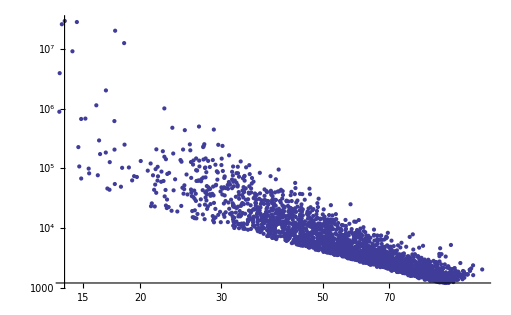

1963.5

20106.2

```mathematica
(* Analyzing correlations between the surface density and the area of a villus *)

surfaceDensityAreaList=Transpose[{surfaceDensityData, areaData}];
surfaceDensityAreaPlot=ListLogLogPlot[surfaceDensityAreaList, PlotRange->All(*{1000,20000}*), Frame->{{1,0},{1,0}}, FrameLabel->{{"Villous area, μm^2", ""},{"Villous surface density, mm^-1",""}},
BaseStyle->{FontSize->20}]


areaFunc[minTerminalVilliRadius]//N
areaFunc[maxTerminalVilliRadius]//N
(*Show[surfaceDensityAreaPlot,
Graphics[{
{Orange,Line[{{0,areaFunc[minTerminalVilliRadius]},{120,areaFunc[minTerminalVilliRadius]}}]},
{Darker[Red],Line[{{0,areaFunc[maxTerminalVilliRadius]},{120,areaFunc[maxTerminalVilliRadius]}}]},
{Darker[Green],Line[{{0,areaFunc[maxNonStemVilliRadius]},{120,areaFunc[maxNonStemVilliRadius]}}]}
}
]]*)

(* Orange - minimal terminal villus,
Red - maximal terminal villus radius,
Green - maximal stem villus radius *)
```

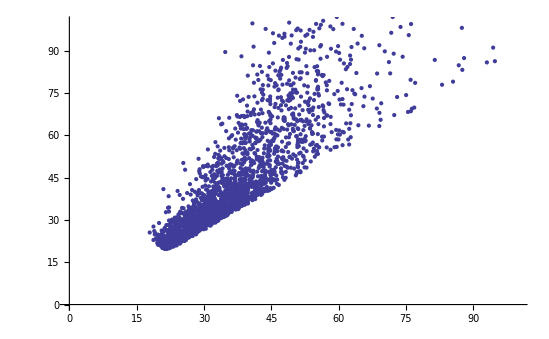

```mathematica
(* Correlating surface density and Subscript[r, S] *)
surfaceDensityRSList=Transpose[{rInData, rSData}];
surfaceDensityRSPlot=ListPlot[surfaceDensityRSList, PlotRange->{{0,100},{0,100}}(*{1000,20000}*), Frame->{{1,0},{1,0}}, FrameLabel->{{"r_S, μm", ""},{"r_in, μm",""}},
BaseStyle->{FontSize->20}]



(*Show[surfaceDensityAreaPlot,
Graphics[{
{Orange,Line[{{0,areaFunc[minTerminalVilliRadius]},{120,areaFunc[minTerminalVilliRadius]}}]},
{Darker[Red],Line[{{0,areaFunc[maxTerminalVilliRadius]},{120,areaFunc[maxTerminalVilliRadius]}}]},
{Darker[Green],Line[{{0,areaFunc[maxNonStemVilliRadius]},{120,areaFunc[maxNonStemVilliRadius]}}]}
}
]]*)

(* Orange - minimal terminal villus,
Red - maximal terminal villus radius,
Green - maximal stem villus radius *)
```

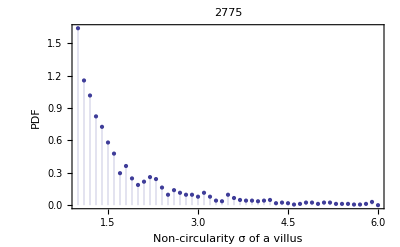

```mathematica
(* Analyzing the circularity of the villi *)
(* Circularity distribution histogram *)
intervalOfInterest={1,6};
selectedσData=Select[σData,#>=intervalOfInterest[[1]]&&#<=intervalOfInterest[[2]]&];
σBinSize={0.1};
distribσ=HistogramDistribution[selectedσData,σBinSize];
pdfσ=PDF[distribσ,s];

pdfσHistogramPlot=DiscretePlot[pdfσ,{s,intervalOfInterest[[1]],intervalOfInterest[[2]],σBinSize[[1]]},PlotRange->All,Frame->{{True,False},{True,False}},FrameLabel->{"Non-circularity σ of a villus","PDF"},BaseStyle->{FontSize->20}, PlotLabel->sectionName]
(*Show[pdfSurfaceDensityHistogramPlot,
Graphics[{
{Orange,Line[{{areaFunc[minTerminalVilliRadius],0},{areaFunc[minTerminalVilliRadius],0.0004}}]},
{Darker[Red],Line[{{areaFunc[maxTerminalVilliRadius],0},{areaFunc[maxTerminalVilliRadius],0.0004}}]},
{Darker[Green],Line[{{areaFunc[maxNonStemVilliRadius],0},{areaFunc[maxNonStemVilliRadius],0.0004}}]}
}
]]*)

(* Orange - minimal terminal villus,
Red - maximal terminal villus radius,
Green - maximal stem villus radius *)
```

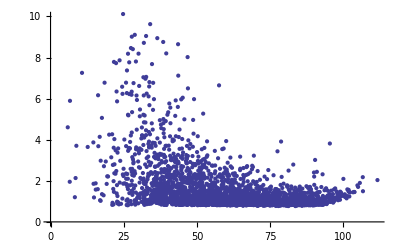

```mathematica
(* Analyzing correlations between the circularity and surface density *)

surfaceDensityCircularityList=Transpose[{surfaceDensityData, σData}];
surfaceDensityCircularityPlot=ListPlot[surfaceDensityCircularityList, PlotRange->{0,10}(*{1000,20000}*), Frame->{{1,0},{1,0}}, FrameLabel->{{"Non-circularity σ of a villus", ""},{"Villous surface density, mm^-1",""}},
BaseStyle->{FontSize->20}]
```

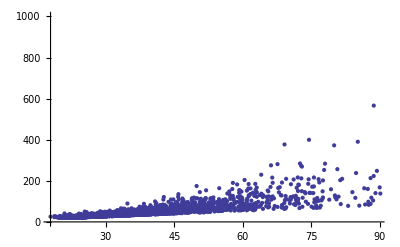

```mathematica
(* Comparing the gluing-invariant radius with the one from the villi area *)
twoRadiiList=Transpose[{rInData, rSData}];
twoRadiiPlot=ListPlot[twoRadiiList, PlotRange->{0,1000}(*{1000,20000}*), Frame->{{1,0},{1,0}}, FrameLabel->{{"r_S, μm^-1", ""},{"r_in, μm^-1",""}},
BaseStyle->{FontSize->20}]
```

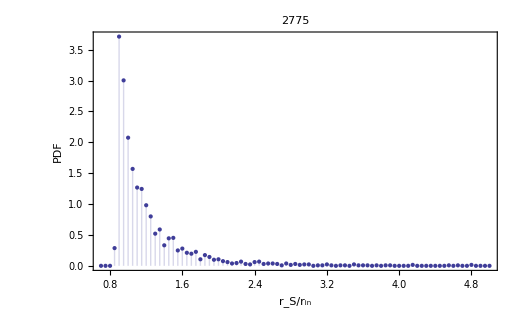

```mathematica
{{(*twoRadiiRatioList=rSData/rInData;
twoRadiiRatioPlot=ListPlot[twoRadiiRatioList, PlotRange->{0,4}(*{1000,20000}*), Frame->{{1,0},{1,0}}, FrameLabel->{{"r_S/r_in", ""},{"Villus number",""}},
BaseStyle->{FontSize->20}]*)}, {□}}
```

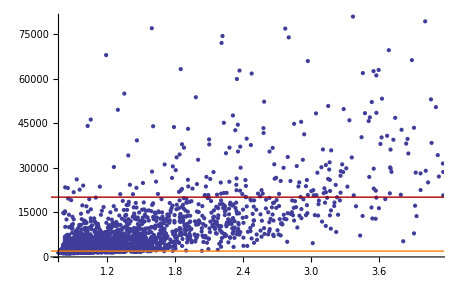

```mathematica
(* Analyzing correlations of the radii ratio and the cross-sectional area *)
radiiRatioAreaList=Transpose[{twoRadiiRatioList^2,areaData}];
radiiRatioAreaPlot=ListPlot[radiiRatioAreaList, PlotRange->{0,8 10^4}, Frame->{{1,0},{1,0}}, FrameLabel->{{"Villi area, μm^2", ""},{"(r_S/r_in)^2",""}},
BaseStyle->{FontSize->20}];

Show[radiiRatioAreaPlot,
Graphics[{
{Orange,Line[{{0, areaFunc[minTerminalVilliRadius]},{6,areaFunc[minTerminalVilliRadius]}}]},
{Darker[Red],Line[{{0,areaFunc[maxTerminalVilliRadius]},{6,areaFunc[maxTerminalVilliRadius]}}]},
{Darker[Green],Line[{{0,areaFunc[maxNonStemVilliRadius]},{6,areaFunc[maxNonStemVilliRadius]}}]}
}
]]

(* Orange - minimal terminal villus,
Red - maximal terminal villus radius,
Green - maximal stem villus radius *)
```